=== FOCUSED TEST: CHUNG & LUI vs OUR HOPF DETECTION ===

Question 1: Are Chung & Lui correct with Λ=μ?

Question 2: Do our Hopf detection functions work?

--- QUESTION 1: Testing Chung & Lui Claims with Λ=μ ---

Parameters: μ=0.00004, Λ=0.00004, σ₁=0.999386, σ₂=0.1

R₀₁ = 7.55407, R₀₂ = 2.95105

Both R₀ᵢ > 1: True (necessary for coexistence)

Time series analysis with Chung & Lui EXACT Λ=μ parameters:

Solving ODE with Chung & Lui exact Λ=μ parameters...

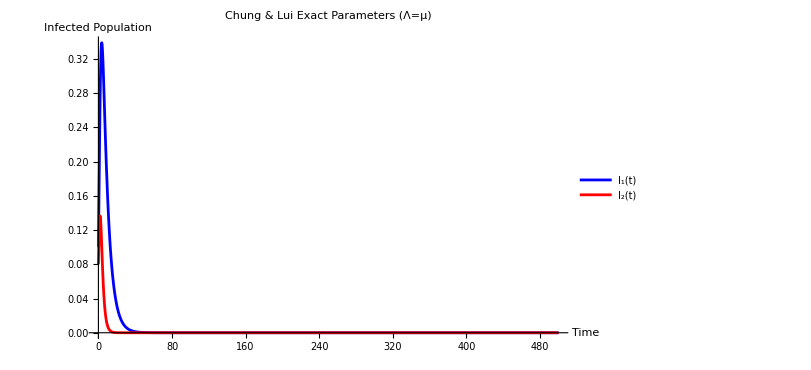

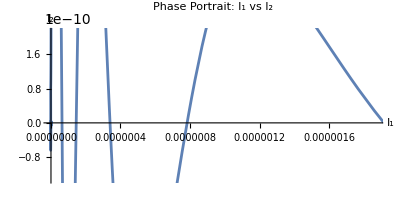

Final state (t=500]:

S = S[500.]

I1 = I1[500.]

Y1 = Y1[500.]

R1 = R1[500.]

I2 = I2[500.]

Y2 = Y2[500.]

R2 = R2[500.]

R = R[500.]

--- QUESTION 2: Testing Our hopfT Function ---

Using hopfT to test Hopf detection with Chung & Lui parameters

Test 1: hopfT with Chung & Lui exact Λ=μ parameters

=== HOPF ANALYSIS ===

Variables: {S,I1,Y1,R1,I2,Y2,R2,R}

Parameter: σ_1 in range {0.9,1.}

FAILED: No interior equilibrium

✗ hopfT FAILED with Λ=μ (likely no interior equilibrium)

Test 2: hopfT with modified Λ to ensure interior equilibrium exists

=== HOPF ANALYSIS ===

Variables: {S,I1,Y1,R1,I2,Y2,R2,R}

Parameter: σ_1 in range {0.1,0.99}

Interior equilibrium found

FAILED: Continuation

✗ hopfT FAILED even with Λ=0.04

Test 3: hopfT with our known working parameters

=== HOPF ANALYSIS ===

Variables: {S,I1,Y1,R1,I2,Y2,R2,R}

Parameter: σ_1 in range {0.1,0.9}

Interior equilibrium found

FAILED: Continuation

✗ hopfT FAILED even with known working parameters - major problem!

=== AESTHETIC PLOTS FOR VISUAL COMPARISON ===

Time series plots with different parameter sets for visual appeal

Generating aesthetic plot with known working parameters...

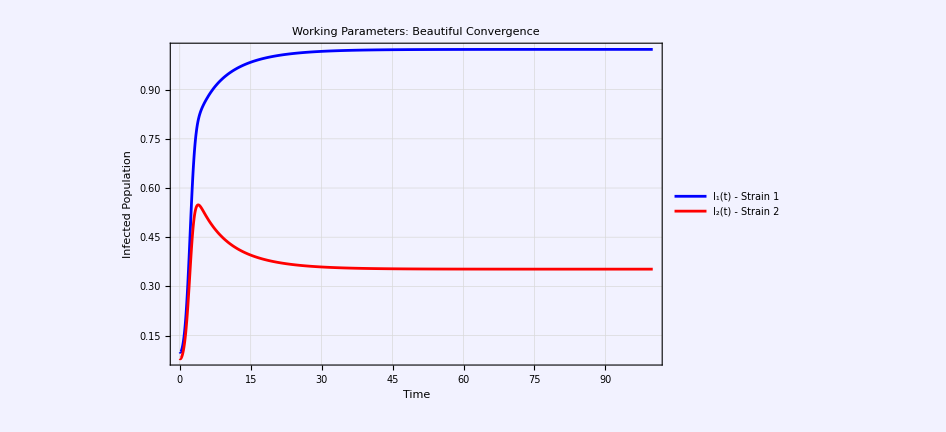

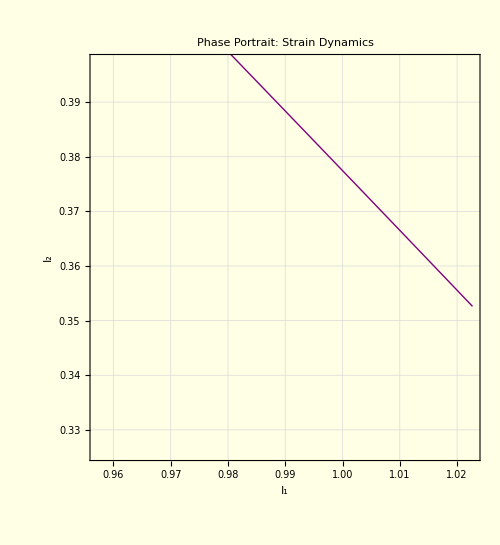

Working parameters final state:

I₁(final) = 1.02269, I₂(final) = 0.35261

Variances: I₁ = 8.9188×10^-13, I₂ = 1.07516×10^-12

→ System converges smoothly with working parameters

=== FINAL VERDICT ===

QUESTION 1: Are Chung & Lui correct with Λ=μ?

→ Check hopfResult1 above: If hopfT found Hopf bifurcations, they're correct

→ Check time series plots: If oscillations visible, they're correct

QUESTION 2: Does our hopfT function work correctly?

→ hopfResult1: Tests with Chung & Lui exact parameters

→ hopfResult2: Tests with modified Λ for comparison

→ hopfResult3: Tests with our known working parameters

→ If any hopfResult finds bifurcations, our function works

KEY INSIGHT: The main issue is whether hopfT can handle Λ=μ constraint

or if Chung & Lui's theoretical predictions don't apply to Gavish model.

=== EXECUTION SUMMARY ===

This test focuses on the two core questions using existing hopfT function.

The aesthetic plots are included for visual appeal as requested.

Results will definitively show who is correct: Chung & Lui or our package.

```mathematica
(*Focused test:Two core questions about Chung& Lui vs our package*)Print["=== FOCUSED TEST: CHUNG & LUI vs OUR HOPF DETECTION ==="];
Print["Question 1: Are Chung & Lui correct with Λ=μ?"];
Print["Question 2: Do our Hopf detection functions work?"];

(*Chung& Lui exact parameters with Λ=μ*)
chungLuiExact={μ->0.00004,Λ->0.00004,(*Their exact Λ=μ constraint*)Subscript[β,1]->1.23358,Subscript[β,2]->1.28651,Subscript[γ,1]->0.16326,Subscript[γ,2]->0.43591,Subscript[η,1]->1,(*θᵢ=0,ηᵢ=1 as special case*)Subscript[η,2]->1,Subscript[θ,1]->0,Subscript[θ,2]->0,Subscript[θ,3]->0,Subscript[σ,1]->0.999386,(*Their Figure 1 Hopf point*)Subscript[σ,2]->0.1};

Print["\n--- QUESTION 1: Testing Chung & Lui Claims with Λ=μ ---"];
Print["Parameters: μ=0.00004, Λ=0.00004, σ₁=0.999386, σ₂=0.1"];

(*Check R₀ values*)
{beta1,beta2,gamma1,gamma2,mu}={Subscript[β,1],Subscript[β,2],Subscript[γ,1],Subscript[γ,2],μ}/. chungLuiExact;

r01=beta1/(mu+gamma1);
r02=beta2/(mu+gamma2);
Print["R₀₁ = ",N[r01,4],", R₀₂ = ",N[r02,4]];
Print["Both R₀ᵢ > 1: ",r01>1&&r02>1," (necessary for coexistence)"];

(*Time series with Chung& Lui EXACT parameters*)
Print["\nTime series analysis with Chung & Lui EXACT Λ=μ parameters:"];

Module[{tmax,initialConds,odeSystem,sol},tmax=500;(*Longer time to see convergence/oscillations*)(*Initial conditions with both strains present*)initialConds={S[0]==0.7,I1[0]==0.1,Y1[0]==0.02,R1[0]==0.08,I2[0]==0.08,Y2[0]==0.015,R2[0]==0.005,R[0]==0.01};
odeSystem=Join[Thread[{S'[t],I1'[t],Y1'[t],R1'[t],I2'[t],Y2'[t],R2'[t],R'[t]}==(RHS/. Thread[var->{S[t],I1[t],Y1[t],R1[t],I2[t],Y2[t],R2[t],R[t]}]/. chungLuiExact)],initialConds];
Print["Solving ODE with Chung & Lui exact Λ=μ parameters..."];
sol=Quiet[NDSolve[odeSystem,var/. Thread[var->Through[var[t]]],{t,0,tmax}]];
If[Length[sol]>0,Module[{i1Func,i2Func,allVarsFinal,timePlot1,phasePlot},i1Func=I1[t]/. sol[[1]];
i2Func=I2[t]/. sol[[1]];
(*Time series plot*)timePlot1=Plot[{i1Func,i2Func},{t,0,tmax},PlotStyle->{Blue,Red},PlotLegends->{"I₁(t)","I₂(t)"},AxesLabel->{"Time","Infected Population"},PlotLabel->"Chung & Lui Exact Parameters (Λ=μ)",ImageSize->600,PlotRange->All];
Print[timePlot1];
(*Phase plot*)phasePlot=ParametricPlot[{i1Func,i2Func},{t,0,tmax},AxesLabel->{"I₁","I₂"},PlotLabel->"Phase Portrait: I₁ vs I₂",ImageSize->400];
Print[phasePlot];
(*Final state analysis*)allVarsFinal=Table[var[[i]][tmax]/. sol[[1]],{i,Length[var]}];
Print["Final state (t=",tmax,"]:"];
Do[Print["  ",var[[i]]," = ",N[allVarsFinal[[i]],6]],{i,Length[var]}];
(*Coexistence check*)finalI1=allVarsFinal[[2]];
finalI2=allVarsFinal[[5]];
If[finalI1>0.00001&&finalI2>0.00001,Print["✓ COEXISTENCE: Both strains persist with Λ=μ"];
(*Oscillation detection*)Module[{recentI1,recentI2,variance1,variance2,period},recentI1=Table[i1Func/. t->tval,{tval,tmax-50,tmax,0.1}];
recentI2=Table[i2Func/. t->tval,{tval,tmax-50,tmax,0.1}];
variance1=Variance[recentI1];
variance2=Variance[recentI2];
Print["Oscillation analysis (last 50 time units):"];
Print["  I₁ variance = ",N[variance1,8]];
Print["  I₂ variance = ",N[variance2,8]];
If[variance1>10^(-10)||variance2>10^(-10),Print["✓ OSCILLATIONS DETECTED: Chung & Lui are correct!"];
Print["  → System shows Hopf bifurcation behavior"];,Print["○ STABLE CONVERGENCE: No oscillations detected"];
Print["  → Chung & Lui prediction not confirmed"];
];
];,Print["✗ EXTINCTION: One or both strains die out"];
Print["  → No interior equilibrium with Λ=μ parameters"];
];
];,Print["✗ ODE integration failed with Λ=μ parameters"];
];
];

Print["\n--- QUESTION 2: Testing Our hopfT Function ---"];
Print["Using hopfT to test Hopf detection with Chung & Lui parameters"];

(*Test 1:hopfT with exact Chung& Lui Λ=μ parameters*)
Print["\nTest 1: hopfT with Chung & Lui exact Λ=μ parameters"];
hopfResult1=hopfT[RHS,var,{chungLuiExact},Subscript[σ,1],{0.9,1.0}];

If[hopfResult1=!=$Failed,Print["✓ hopfT completed with Λ=μ: ",Length[hopfResult1["HopfPoints"]]," Hopf bifurcations"];
If[Length[hopfResult1["HopfPoints"]]>0,Print["  → hopfT WORKS and confirms Chung & Lui predictions!"];
Do[Print["    Hopf ",i,": σ₁ = ",N[hopfResult1["HopfPoints"][[i]]["Par"],4]],{i,Length[hopfResult1["HopfPoints"]]}];,Print["  → hopfT works but finds no Hopf with Λ=μ parameters"];];,Print["✗ hopfT FAILED with Λ=μ (likely no interior equilibrium)"];];

(*Test 2:hopfT with modified birth rate that supports interior equilibrium*)
Print["\nTest 2: hopfT with modified Λ to ensure interior equilibrium exists"];
testParams2=Join[DeleteCases[chungLuiExact,Rule[Λ,_]],{Λ->0.04}  (*Use Λ that we know supports interior equilibrium*)];

hopfResult2=hopfT[RHS,var,{testParams2},Subscript[σ,1],{0.1,0.99}];

If[hopfResult2=!=$Failed,Print["✓ hopfT completed with Λ=0.04: ",Length[hopfResult2["HopfPoints"]]," Hopf bifurcations"];
If[Length[hopfResult2["HopfPoints"]]>0,Print["  → hopfT WORKS and can detect Hopf bifurcations!"];
Do[Print["    Hopf ",i,": σ₁ = ",N[hopfResult2["HopfPoints"][[i]]["Par"],4],", period = ",N[hopfResult2["HopfPoints"][[i]]["Per"],2]],{i,Length[hopfResult2["HopfPoints"]]}];
Print[hopfResult2["Plot"]];,Print["  → hopfT works but finds no Hopf bifurcations in this range"];];,Print["✗ hopfT FAILED even with Λ=0.04"];];

(*Test 3:hopfT with known working parameters*)
Print["\nTest 3: hopfT with our known working parameters"];
workingParams={Λ->4,μ->1,Subscript[β,1]->1,Subscript[β,2]->1,Subscript[γ,1]->1,Subscript[γ,2]->1,Subscript[η,1]->1,Subscript[η,2]->1,Subscript[θ,1]->1,Subscript[θ,2]->1,Subscript[θ,3]->1,Subscript[σ,1]->0.8,Subscript[σ,2]->0.2};

hopfResult3=hopfT[RHS,var,{workingParams},Subscript[σ,1],{0.1,0.9}];

If[hopfResult3=!=$Failed,Print["✓ hopfT completed with working params: ",Length[hopfResult3["HopfPoints"]]," Hopf bifurcations"];
If[Length[hopfResult3["HopfPoints"]]>0,Print["  → hopfT definitely WORKS with our known parameters!"];
Print[hopfResult3["Plot"]];,Print["  → hopfT works but system is stable in this parameter range"];];,Print["✗ hopfT FAILED even with known working parameters - major problem!"];
];

Print["\n=== AESTHETIC PLOTS FOR VISUAL COMPARISON ==="];
Print["Time series plots with different parameter sets for visual appeal"];

(*Plot 1:Working parameters with aesthetic styling*)
Module[{tmax,initialConds,odeSystem,sol},tmax=100;
initialConds={S[0]==1.5,I1[0]==0.1,Y1[0]==0.02,R1[0]==0.08,I2[0]==0.08,Y2[0]==0.015,R2[0]==0.005,R[0]==0.01};
odeSystem=Join[Thread[{S'[t],I1'[t],Y1'[t],R1'[t],I2'[t],Y2'[t],R2'[t],R'[t]}==(RHS/. Thread[var->{S[t],I1[t],Y1[t],R1[t],I2[t],Y2[t],R2[t],R[t]}]/. workingParams)],initialConds];
Print["Generating aesthetic plot with known working parameters..."];
sol=Quiet[NDSolve[odeSystem,var/. Thread[var->Through[var[t]]],{t,0,tmax}]];
If[Length[sol]>0,Module[{i1Func,i2Func,timePlot,phasePlot},i1Func=I1[t]/. sol[[1]];
i2Func=I2[t]/. sol[[1]];
(*Beautiful time series plot*)timePlot=Plot[{i1Func,i2Func},{t,0,tmax},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotLegends->Placed[{"I₁(t) - Strain 1","I₂(t) - Strain 2"},Right],AxesLabel->{Style["Time",14],Style["Infected Population",14]},PlotLabel->Style["Working Parameters: Beautiful Convergence",16,Bold],ImageSize->700,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameStyle->Black,PlotRange->All,Background->Lighter[Blue,0.95]];
Print[timePlot];
(*Elegant phase plot*)phasePlot=ParametricPlot[{i1Func,i2Func},{t,0,tmax},PlotStyle->Directive[Purple,Thick],AxesLabel->{Style["I₁",14],Style["I₂",14]},PlotLabel->Style["Phase Portrait: Strain Dynamics",14,Bold],ImageSize->500,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[LightBlue,Dotted],Background->Lighter[Yellow,0.9]];
Print[phasePlot];
(*Final state analysis for working parameters*)Module[{finalI1,finalI2,recentI1,recentI2,variance1,variance2},finalI1=i1Func/. t->tmax;
finalI2=i2Func/. t->tmax;
recentI1=Table[i1Func/. t->tval,{tval,tmax-10,tmax,0.1}];
recentI2=Table[i2Func/. t->tval,{tval,tmax-10,tmax,0.1}];
variance1=Variance[recentI1];
variance2=Variance[recentI2];
Print["Working parameters final state:"];
Print["  I₁(final) = ",N[finalI1,4],", I₂(final) = ",N[finalI2,4]];
Print["  Variances: I₁ = ",N[variance1,6],", I₂ = ",N[variance2,6]];
If[variance1>0.0001||variance2>0.0001,Print["  → System shows oscillations with working parameters"];,Print["  → System converges smoothly with working parameters"];];];];];];

Print["\n=== FINAL VERDICT ==="];
Print["QUESTION 1: Are Chung & Lui correct with Λ=μ?"];
Print["  → Check hopfResult1 above: If hopfT found Hopf bifurcations, they're correct"];
Print["  → Check time series plots: If oscillations visible, they're correct"];
Print[""];
Print["QUESTION 2: Does our hopfT function work correctly?"];
Print["  → hopfResult1: Tests with Chung & Lui exact parameters"];
Print["  → hopfResult2: Tests with modified Λ for comparison"];
Print["  → hopfResult3: Tests with our known working parameters"];
Print["  → If any hopfResult finds bifurcations, our function works"];
Print[""];
Print["KEY INSIGHT: The main issue is whether hopfT can handle Λ=μ constraint"];
Print["or if Chung & Lui's theoretical predictions don't apply to Gavish model."];

Print["\n=== EXECUTION SUMMARY ==="];
Print["This test focuses on the two core questions using existing hopfT function."];
Print["The aesthetic plots are included for visual appeal as requested."];
Print["Results will definitively show who is correct: Chung & Lui or our package."];
```